```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{8}]];
hmfi = Interpolation[{#[[1]],#[[2]],#[[3]]}&/@hmf];
dotMi = Interpolation[{#[[1]],#[[2]],#[[4]]}&/@hmf];
DdotMi = Interpolation[{#[[1]],#[[2]],#[[5]]}&/@hmf,InterpolationOrder->1];
phiUVi = Interpolation[{#[[1]],#[[6]],#[[8]]}&/@hmf,InterpolationOrder->1];
AUVi = Interpolation[{#[[1]],#[[6]],#[[7]]}&/@hmf,InterpolationOrder->1];
```

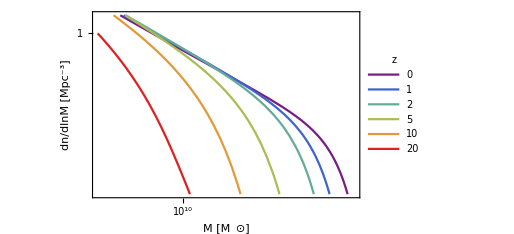

```mathematica
Plot[Log10[10^9hmfi[#,10^logM]]&/@{0.01,1,2,5,10,20}//Evaluate,{logM,7,Log10@hmfi[[1,2,2]]},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,5]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,1,2,5,10,20},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]]
```

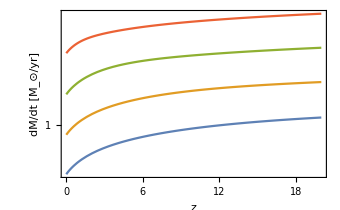

```mathematica
Plot[10^-6*dotMi[z,10^#]&/@Range[8,14,2]//Log10//Evaluate,{z,dotMi[[1,1,1]],20},FrameLabel->{"z","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340]
```

```mathematica
HSTdata = Import[NotebookDirectory[]<>"UVLF_HST.txt","Table"];
ΦHST[z_]:=Select[HSTdata[[3;;-1]],#[[1]]==z&][[All,{2,4,5}]]
```

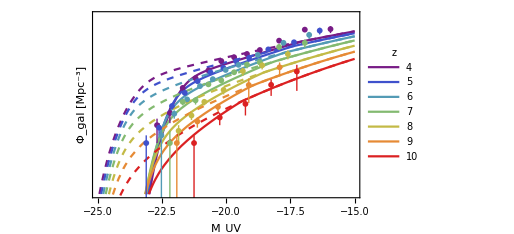

```mathematica
Show[Plot[Log10[10^9phiUVi[#,m-AUVi[#,m]]]&/@{4,5,6,7,8,9,10}//Evaluate,{m,-26,-15},PlotRange->{{-25,-15},{-8,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6]),ImageSize->380,PlotLegends->LineLegend[Automatic,{4,5,6,7,8,9,10},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
Plot[Log10[10^9phiUVi[#,m]]&/@{4,5,6,7,8,9,10}//Evaluate,{m,-26,-15},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,6])],
ListPlot[Table[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[3]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@ΦHST[z],{z,{4,5,6,7,8,9,10}}]//Evaluate,PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6])]]
```

```mathematica
Plnmulist = ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]];
zlist = DeleteDuplicates[Plnmulist[[All,1]]]
Plnmulist =GatherBy[Plnmulist,First][[All,All,{2,3}]];
```

{0.2,0.5,1,1.5,2,3,4,5,6,7,8,9,10,12,15,20}

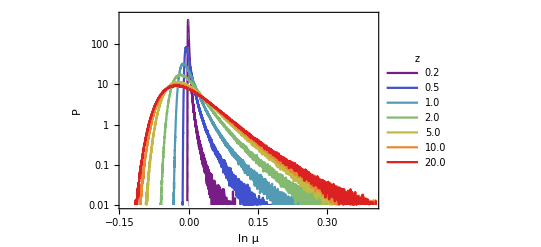

```mathematica
ListLogPlot[Plnmulist[[{1,2,3,5,8,13,16}]],Joined->True,PlotRange->{{-0.14,0.4},{0.01,500}},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"ln μ","P"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6]),PlotLegends->LineLegend[Automatic,{"0.2","0.5","1.0","2.0","5.0","10.0","20.0"},LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]]]
```

```mathematica
Plnmui = Interpolation[ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]],InterpolationOrder->1];
```

```mathematica
phiUV2 = ParallelTable[{#,Quiet@NIntegrate[phiUVi[zlist[[jz]],#-AUVi[zlist[[jz]],#]+Log[10]lnmu]Plnmui[zlist[[jz]],lnmu],{lnmu,-0.1,0.5},Method->"AdaptiveMonteCarlo"]}&/@Subdivide[-24.,-15,31],{jz,Length@zlist}];
```

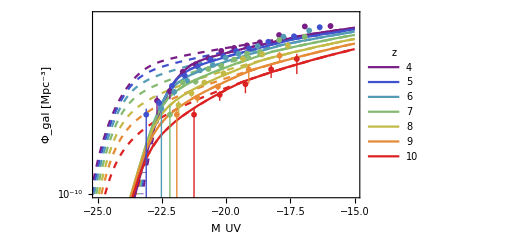

```mathematica
Show[Plot[Log10[10^9phiUVi[#,m-AUVi[#,m]]]&/@{4,5,6,7,8,9,10}//Evaluate,{m,-26,-15},PlotRange->{{-25,-15},{-10,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->(Directive[ColorData["Rainbow"][#],DotDashed]&/@Subdivide[0,1,6]),ImageSize->380],
Plot[Log10[10^9phiUVi[#,m]]&/@{4,5,6,7,8,9,10}//Evaluate,{m,-26,-15},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,6])],
ListPlot[Table[{#[[1]],Log10[10^9#[[2]]]}&/@phiUV2[[j]],{j,Range[7,13,1]}],Joined->True,PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6]),PlotLegends->LineLegend[Automatic,{4,5,6,7,8,9,10},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
ListPlot[Table[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[3]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@ΦHST[z],{z,{4,5,6,7,8,9,10}}]//Evaluate,PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6])]]
```